```mathematica
(*vorts=("vorts"<>ToString[#]<>"_optimized_parallelsearch"&)/@Range[99];*)
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>vorts[[1]]<>".xml"];*)
```

```mathematica
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_Rainbow9_diagonal.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

(* nucleon 0.1 0.3 0.6 vortex 1/3 1/3 1/3 *)
(*targets=<|2->{0.2,0.8},3->{1/3.,1/3.,1/3.},4->{0.1,0.2,0.3,0.4}|>;*)
(*targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;*)
(*target=targets[Length[index0]]*)
CloseKernels[];
LaunchKernels[];
Clear[f];
Clear[data];
records={};
epsilon=0.03;
stepsize=0.05;
iterationcount1=80;
iterationcount2=40;
targets={ConstantArray[1./Length@index,Length@index],intensity0[[#]]&/@index0//#/Total[#]&,alpha0[[#]]&/@index0//#/Total[#]&};
target=targets[[3]];(* 1 even, 2 diagonal, 3 opacity as target *)
legends=MapIndexed["feature"<>ToString@First@#2&,index];
Length@features==Length@legends
```

True

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
VisibilityField[fun_]:=Module[{vis},
vis=Block[{f=fun,data=d},renderslices2[face]]
]
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
margin=4;
mrms=0;
mindex=0;
iteration=0;
t2=0;
t1=AbsoluteTime[];
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
gradient=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tfixed\t","converge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\t<",epsilon]];
If[rms<mrms || mrms==0,mrms=rms;mindex=iterator];
If[t2==0&&mindex+margin<iterator,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tfixed\t","diverge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\tmindex\t",mindex,"\tmrms\t",mrms]];
If[t2==0&&iterator==iterationcount1,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tfixed\t","max\t",t2-t1,"\t",iterator,"\trms\t",rms]];
{mean,peaks0,rms,steps}
],{iterator,iterationcount1}];
```

nucleon_Rainbow9_diagonal	fixed	max	5.8500375	iteration	80	rms	0.0526457

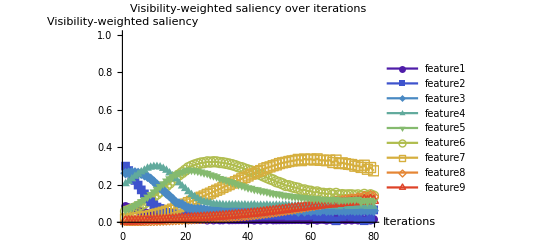

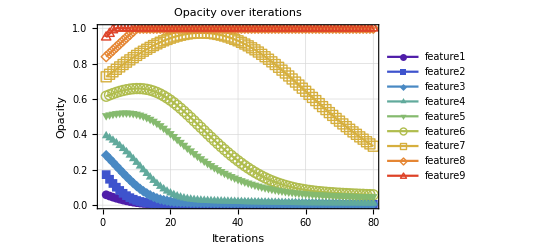

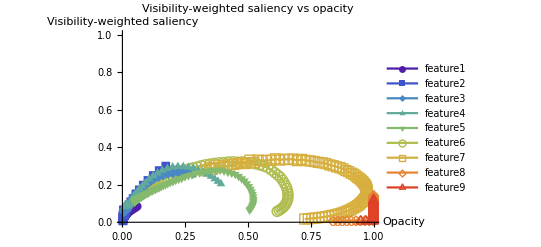

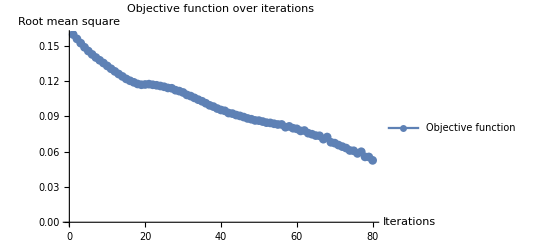

{5.8500375,80,{0.00264974,0.00476858,0.00662896,0.011467,0.0482928,0.058499,0.333125,1.,1.},80,0.0526457}

```mathematica
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_fixed.pdf",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"},BaseStyle->{FontSize->14},PlotTheme->"Detailed"]
Export[plotpath<>dataname<>"_opacity_fixed.pdf",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_fixed.pdf",saliencyopacity1];
rmslist1=#3&@@@list;
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_fixed.pdf",rms1];
path1=#2&@@@list;
minstep1=First@FirstPosition[rmslist1,_?(#==Min[rmslist1]&)];
AppendTo[records,{t2-t1,iteration,path1[[minstep1]],minstep1,rmslist1[[minstep1]]}];
{t2-t1,iteration,path1[[minstep1]],minstep1,rmslist1[[minstep1]]}
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Objective Function","Steps"}},TableSpacing->{2,1}];
Export[plotpath<>dataname<>"_table_fixed.pdf",table1];
```

```mathematica
(*rmslists1=ListLinePlot[{rmslist1,rmslist5},PlotLegends->{"Method 1","Method 2"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_newton.png",rmslists1];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
margin=4;
mrms=0;
mindex=0;
iteration=0;
t2=0;
t1=AbsoluteTime[];
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex,minrms},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
(*rms=RootMeanSquare[mean-target];*)
rms=If[Norm[previous]>0,minrms,RootMeanSquare[mean-target]];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
minrms=rmslist[[minindex]];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tparallelsearch\t","converge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\t<",epsilon]];
If[rms<mrms || mrms==0,mrms=rms;mindex=iterator];
If[t2==0&&mindex+margin<iterator,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tparallelsearch\t","diverge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\tmindex\t",mindex,"\tmrms\t",mrms]];
If[t2==0&&iterator==iterationcount2,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tparallelsearch\t","max\t",t2-t1,"\t",iterator,"\trms\t",rms]];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,iterationcount2}];
```

nucleon_Rainbow9_diagonal	parallelsearch	converge	44.5691652	iteration	28	rms	0.027763	<0.03

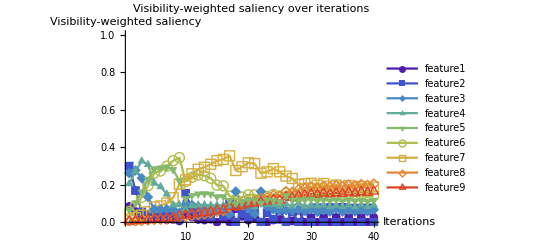

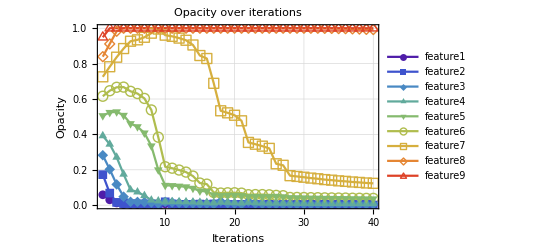

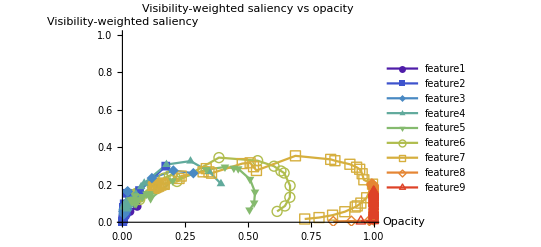

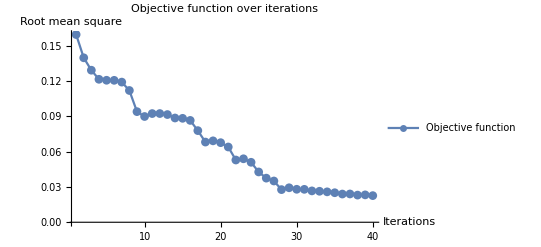

{44.5691652,28,{0.00309976,0.000606689,0.00606491,0.00874347,0.0357298,0.0384451,0.12346,0.99239,1.},40,0.0226528}

```mathematica
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_parallelsearch.pdf",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"},BaseStyle->{FontSize->14},PlotTheme->"Detailed"]
Export[plotpath<>dataname<>"_opacity_parallelsearch.pdf",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_parallelsearch.pdf",saliencyopacity2];
rmslist2=#3&@@@list;
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_parallelsearch.pdf",rms2];
path2=#2&@@@list;
minstep2=First@FirstPosition[rmslist2,_?(#==Min[rmslist2]&)];
AppendTo[records,{t2-t1,iteration,path2[[minstep2]],minstep2,rmslist2[[minstep2]]}];
{t2-t1,iteration,path2[[minstep2]],minstep2,rmslist2[[minstep2]]}
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Objective Function","Steps","Multiplier(γ)"}},TableSpacing->{2,1}];
Export[plotpath<>dataname<>"_table_parallelsearch.pdf",table2];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
margin=4;
mrms=0;
mindex=0;
iteration=0;
t2=0;
t1=AbsoluteTime[];
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
(*rms=RootMeanSquare[mean-target];*)
rms=If[Norm[previous]>0,minrms,RootMeanSquare[mean-target]];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tlinesearch\t","converge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\t<",epsilon]];
If[rms<mrms || mrms==0,mrms=rms;mindex=iterator];
If[t2==0&&mindex+margin<iterator,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tlinesearch\t","diverge\t",t2-t1,"\t",iterator,"\trms\t",rms,"\tmindex\t",mindex,"\tmrms\t",mrms]];
If[t2==0&&iterator==iterationcount2,t2=AbsoluteTime[];iteration=iterator;Print[dataname,"\tlinesearch\t","max\t",t2-t1,"\t",iterator,"\trms\t",rms]];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,iterationcount2}];
```

nucleon_Rainbow9_diagonal	linesearch	converge	6.5676421	iteration	30	rms	0.0288108	<0.03

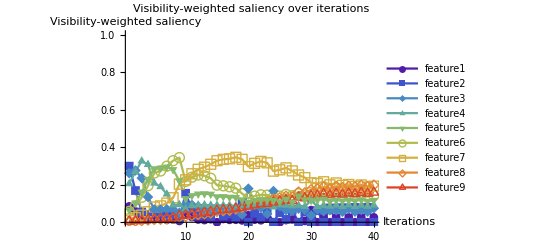

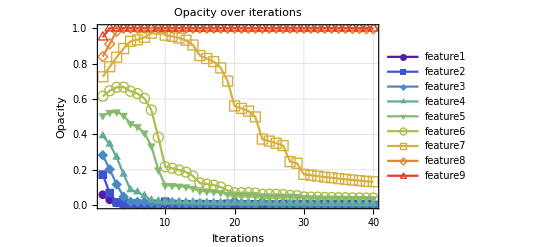

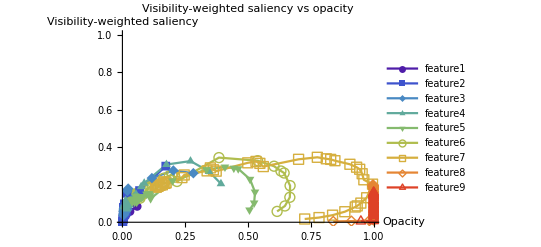

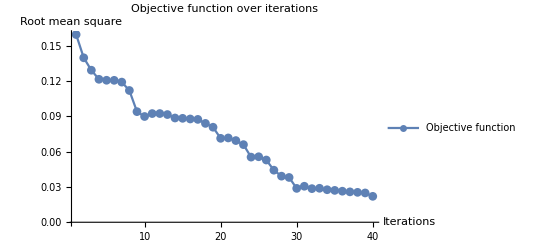

{6.5676421,30,{0.00320825,0.000546355,0.00627362,0.00891133,0.0369219,0.0400524,0.132339,0.996523,1.},40,0.0220498}

```mathematica
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_linesearch.pdf",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"},BaseStyle->{FontSize->14},PlotTheme->"Detailed"]
Export[plotpath<>dataname<>"_opacity_linesearch.pdf",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_linesearch.pdf",saliencyopacity3];
rmslist3=#3&@@@list;
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_linesearch.pdf",rms3];
path3=#2&@@@list;
minstep3=First@FirstPosition[rmslist3,_?(#==Min[rmslist3]&)];
AppendTo[records,{t2-t1,iteration,path3[[minstep3]],minstep3,rmslist3[[minstep3]]}];
{t2-t1,iteration,path3[[minstep3]],minstep3,rmslist3[[minstep3]]}
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Objective Function","Steps","Multiplier(γ)"}},TableSpacing->{2,1}];
Export[plotpath<>dataname<>"_table_linesearch.pdf",table3];
```

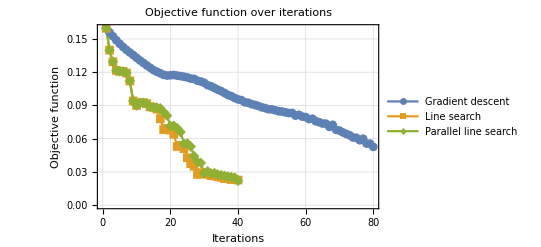

```mathematica
rmslists2=ListLinePlot[{rmslist1,rmslist2,rmslist3},PlotLegends->{"Gradient descent","Line search","Parallel line search"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"},BaseStyle->{FontSize->14},PlotTheme->"Detailed"]
Export[plotpath<>dataname<>"_rms_fixed_linesearch_parallel.pdf",rmslists2];
```

```mathematica
(*(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
(*steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*stepsize,-gradient*stepsize]
]];*)
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*gradient*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,70}];*)
```

```mathematica
(*t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_difference.png",table4];
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];*)
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
recordxml=plotpath<>"records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

nucleon_Rainbow9_diagonal→{{5.8500375,80,{0.00264974,0.00476858,0.00662896,0.011467,0.0482928,0.058499,0.333125,1.,1.},80,0.0526457},{44.5691652,28,{0.00309976,0.000606689,0.00606491,0.00874347,0.0357298,0.0384451,0.12346,0.99239,1.},40,0.0226528},{6.5676421,30,{0.00320825,0.000546355,0.00627362,0.00891133,0.0369219,0.0400524,0.132339,0.996523,1.},40,0.0220498}}

```mathematica
ObjectiveFunction[pos_]:=RootMeanSquare[VisibilitySaliency[pos]-target];
```

```mathematica
(*ObjectiveFunction[{0.1,0.3,0.6}]
(*FindMinimum[{ObjectiveFunction[{x1,x2,x3}],0≤x1≤1,0≤x2≤1,0≤x3≤1},{{x1,{0.1}},{x2,{0.3}},{x3,{0.6}}}]*)
FindMinimum[x1 Cos[x1]+x2 Cos[x2],{{x1,0},{x2,0}}]
Plot3D[x1 Sin[x1]+x2 Sin[x2],{x1,0,10},{x2,0,10}]*)
```

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[plotpath<>dataname<>"_parameterspace.png",sp];
Export[plotpath<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[plotpath<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xmlobject},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xmlobject=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function created using Wolfram Mathematica"]},VoreenData,{}];
Export[filename,xmlobject, "XML"];
rgbafunction2
];
```

```mathematica
{path1[[minstep1]],path2[[minstep2]],path3[[minstep3]]}//TableForm[#,TableHeadings->{Automatic, legends}]&
```

| feature1 | feature2 | feature3 | feature4 | feature5 | feature6 | feature7 | feature8 | feature9
1 | 0.00264974 | 0.00476858 | 0.00662896 | 0.011467 | 0.0482928 | 0.058499 | 0.333125 | 1. | 1.
2 | 0.00309976 | 0.000606689 | 0.00606491 | 0.00874347 | 0.0357298 | 0.0384451 | 0.12346 | 0.99239 | 1.
3 | 0.00320825 | 0.000546355 | 0.00627362 | 0.00891133 | 0.0369219 | 0.0400524 | 0.132339 | 0.996523 | 1.

```mathematica
fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
VisibilitySaliency[path1[[minstep1]]]//AbsoluteTiming
Visibility[fun]//AbsoluteTiming
VisibilityField[fun]//AbsoluteTiming
```

{0.0741988,{0.0151378,0.0655155,0.0613459,0.0840242,0.108856,0.139296,0.274054,0.136247,0.115522}}

{0.0735557,{0.,0.0661458,0.0580092,0.0829588,0.114244,0.140239,0.184319,0.196302,0.157782}}

{0.0546943,-Graphics3D-}

```mathematica
(*Table[VisibilitySaliency[path1[[minstep1]]]//AbsoluteTiming,{i,10}]//Mean@First@Transpose[#]&*)
```

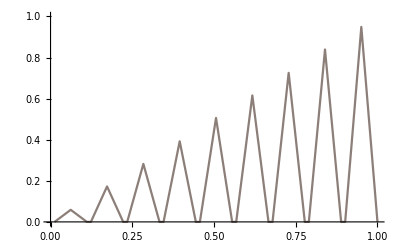

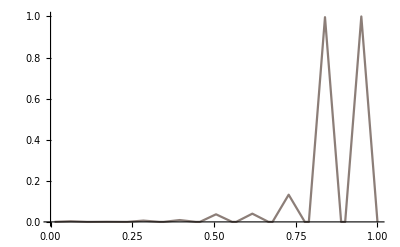

```mathematica
tf1=saveTransferFunction[path1[[minstep1]],plotpath<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[path2[[minstep2]],plotpath<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[path3[[minstep3]],plotpath<>dataname<>"_optimized_linesearch.tfi"];
(*tf5=saveTransferFunction[path5[[minstep5]],plotpath<>dataname<>"_optimized_newton.tfi"];*)

Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]];
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]];
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

Part::pspec1: Part specification NotFound is not applicable.

Part::partw: Part 3 of {{0.0588235,0.172549,0.282353,0.392157,0.505882,0.615686,0.72549,0.839216,0.94902},{0.051684,0.146442,0.262437,0.380286,0.510479,0.623468,0.739736,0.857267,0.969378},«48»,«30»}⟦NotFound⟧ does not exist.

Part::partw: Part 4 of {{0.0588235,0.172549,0.282353,0.392157,0.505882,0.615686,0.72549,0.839216,0.94902},{0.051684,0.146442,0.262437,0.380286,0.510479,0.623468,0.739736,0.857267,0.969378},«48»,«30»}⟦NotFound⟧ does not exist.

Part::partw: Part 5 of {{0.0588235,0.172549,0.282353,0.392157,0.505882,0.615686,0.72549,0.839216,0.94902},{0.051684,0.146442,0.262437,0.380286,0.510479,0.623468,0.739736,0.857267,0.969378},«48»,«30»}⟦NotFound⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pspec1: Part specification NotFound is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

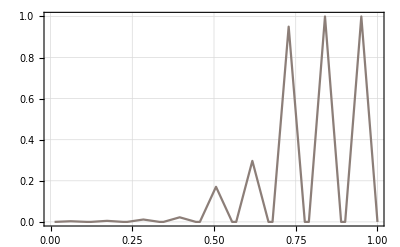
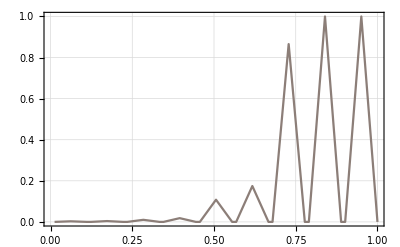
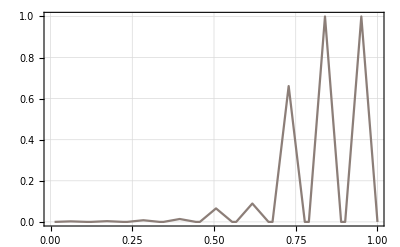
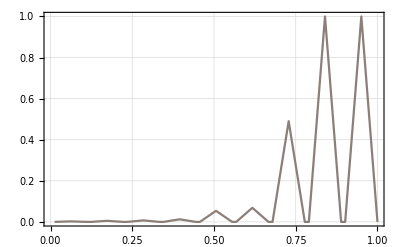
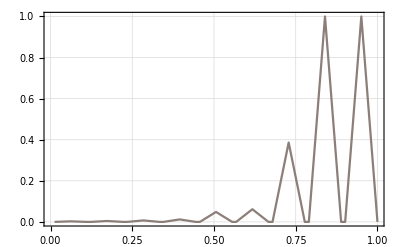
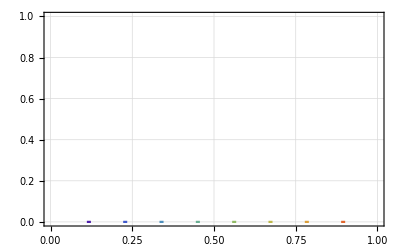
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* optimization with different rms thresholds *)
Table[Module[{index,tf0},
index=First@FirstPosition[rmslist1,_?(#<rmsthreshold&)];
tf0=saveTransferFunction[path1[[index]],NotebookDirectory[]<>"rms_threshold\\"<>dataname<>"_optimized_fixed_"<>ToString[rmsthreshold]<>".tfi"];
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"rms<"<>ToString[rmsthreshold],PlotTheme->"Detailed"]
],{rmsthreshold,{0.1,0.09,0.08,0.07,0.06,0.05,0.04,0.03,0.02,0.01}}]
```

```mathematica
(*(* x(k+1)=x(k)-(f-f0)/(f'-f0') *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size (second order similar to Newton's) *)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,direction,square},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square:=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=Normalize[dy/dx]*Norm[gradient];-direction*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,iterationcount1}];*)
```

```mathematica
(*saliency5=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_newton.png",saliency5];
opacity5=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_newton.png",opacity5];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity5=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_newton.png",saliencyopacity5];
rmslist5=#3&@@@list;
rms5=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_newton.png",rms5];
path5=#2&@@@list;
minstep5=First@FirstPosition[rmslist5,_?(#==Min[rmslist5]&)];
AppendTo[records,{t2-t1,iteration,path5[[minstep5]],minstep5,rmslist5[[minstep5]]}];
{t2-t1,iteration,path5[[minstep5]],minstep5,rmslist5[[minstep5]]}
table5=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Objective Function","Steps"}},TableSpacing->{2,1}]
Export[plotpath<>dataname<>"_table_newton.png",table5];*)
```